The Mathematica^®Journal

# Visualizing Complex Functions with the Presentations Application

Murray Eisenberg
David J. M. Park, Jr.

Visualization is an invaluable companion to symbolic computation in understanding the complex plane and complex-valued functions of a complex variable. The Presentations application, an add-on to Mathematica, provides a rich set of tools for assisting such visualization. This article demonstrates some capabilities of the application, especially those relevant in an introduction to complex analysis, and it indicates some teaching and learning issues that arise. Included are examples of how complex functions map objects in the complex plane and on the Riemann sphere, and of how complex functions behave near singularities and at branch points.

## Introduction

Visualization and symbolic computation are both essential to understanding how functions behave. Visualizing the behavior of a real-valued function of a real variable is often easy because the function’s graph may be plotted in the plane—a space with just two real dimensions. On the other hand, visualizing the behavior of a complex-valued function of a complex variable is more difficult because the graph lives in a space with four real dimensions. Whereas Mathematica is replete with resources for symbolic computation with complex functions, out of the box it provides only a meager set of tools for visualizing such functions. To do much more than what is provided by the two-parameter form of ParametricPlot—the replacement for the standard add-on package Graphics`ComplexMap`—even to plot the image of a simple curve in the complex plane requires the effort of constructing the image set and its graphical representation and then combining the graphics objects. The Presentations application [1], written by the second author, is a purchasable add-on to Mathematica that provides, among many other things, a rich set of tools for plotting complex functions and some utilities for complex symbolic computation. Presentations includes full documentation with individual help pages and examples for each command.

Presentations is the successor to both the Cardano3 [2] and DrawGraphics [1] applications. In a Mathematica-enriched introductory complex analysis course, the first author prepared demonstration and exercise notebooks for Cardano3 [3] and experimented with students’ using it; experience there led to some enhancement of the application. The course used the textbook by Mathews and Howell [4], which is fairly traditional in approach, although it does go a bit further than some introductions in emphasizing mapping properties of complex functions. Presentations would be especially suitable for use with a less traditional, more visually oriented text, such as the one by Needham [5], which inspired and helped guide development of the application.

In this article we demonstrate some capabilities of the Presentations package ComplexGraphics, especially those relevant in an introduction to complex analysis. The examples include a geometric problem solved by complex means, representations of complex functions as mappings, depiction of singularities, analysis of branch points, and a visualization of the Argument Principle. Typically the examples include embellishments that might be inappropriate for a novice at both Mathematica and complex analysis to program, but these embellishments illustrate some of the advanced functionality of the packages.

Various graphical representations of complex functions are often needed to emphasize their various features. DrawCartesianMap and DrawPolarMap plots within Draw2D expressions can be used to emphasize mapping properties. Riemann sphere plots can be used to better depict behavior near the point at infinity, or to emphasize periodic behavior. ComplexDensityDraw and other domain-coloring plots give an overall representation of a function in the plane that emphasizes singular points and branch lines.

Representing complex values as vectors is one method for obtaining a four-dimensional picture—two dimensions in the plane and two dimensions in each vector. By moving a single vector as a Locator around the domain, we can see how a function varies along a path; superimposing the moving vector upon a background ComplexPolarContour plot of the modulus provides even further visual information. This visual information can be accompanied by panels giving dynamically changing numerical values. More generally, dynamic interactivity is especially effective in making various properties come alive. Presentations can give an overall picture or zoom in on particular portions of the domain. Multifunctions can be used with several of the plot types. All these techniques increase our ability to understand complex function behavior.

Top-level Presentations complex graphics functions ultimately call upon more general graphing routines like those in DrawGraphics, which is discussed in [6]; the Presentations graphing routines, in turn, ultimately call built-in Mathematica functions. To reproduce all the results in this notebook, in addition to Mathematica and Presentations, will also require Ersek’s RootSearch package [7].

Only some of the functionality of Presentations is illustrated here, even for complex functions. Visualizations of Riemann surfaces are discussed in [8]. Online resources for visualizing complex functions are available that do not involve Mathematica at all; see [9], for example.

This article is based upon the authors’ original paper [10] for the eighth International Mathematica Symposium (IMS’06) that used Cardano3. Thanks to the advances in Mathematica 6 and the concomitant development of the application, the examples here go well beyond what was possible before.

## Initialization

To begin, we initialize the Presentations application.

```mathematica
Needs["Presentations`Master`"]
```

To open the documentation for Presentations directly, evaluate the following input cell.

```mathematica
PresentationsHelp
```

The function styleText will be used in several places to format point labels.

```mathematica
styleText[txt_,z_,offset_:{0,0}]:=
Style[ComplexText[TraditionalForm[txt],z,offset],FontSize->12,Bold];
```

## Geometry in the Complex Plane

Presentations contains a complete set of graphics primitives that directly use complex numbers for points. Geometrical diagrams are an important part of mathematical discussions, yet students find it difficult to draw such diagrams. The power of complex algebra is that many such diagrams are more easily constructed and drawn in the complex plane. Such diagrams are not only an excellent introduction to Presentations and complex algebra, but also a valuable technique for mathematical work.

The problem considered here is from a posting on MathGroup [11] (with Greek letters used for the angle variables of the original):

I am trying to find the angle β corresponding to the points on the circumference of the circle (5+8Cos[β],7+8Sin[β]) that are a distance of 7 units from a point on the circumference of the circle (13Cos[α],13Sin[α]) for angles α in the first quadrant.

The following creates a diagram for the problem.

```mathematica
With[{c=5+7ⅈ,r1=8,r2=13,β1=60°,α1=25°},
Draw2D[
{ComplexCurve[c+r1 ⅇ^(ⅈ β),{β,0,2π}],
Red,ComplexCurve[r2 ⅇ^(ⅈ α),{α,0,π/2}],
Gray,ComplexLine[{c,c+r1}],
ComplexLine[{c,c+r1 ⅇ^(ⅈ β1)}],
ComplexLine[{0,r2 ⅇ^(ⅈ α1)}],
Blue,ComplexLine[{r2 ⅇ^(ⅈ α1),c+r1 ⅇ^(ⅈ β1)}],
Black,ComplexText["β",c+r1/5 ⅇ^(ⅈ β1/2)],
ComplexText["α",r2/5 ⅇ^(ⅈ α1/2)],
ComplexCirclePoint[c,3,Black,Legacy@Linen],
ComplexCirclePoint[#,3,Black,Legacy@Peacock]& /@{c+r1 ⅇ^(ⅈ β1),r2 ⅇ^(ⅈ α1)}},
Axes->True,Ticks->None,
PlotLabel->"Geometry Problem",
ImageSize->Scaled[0.4]]
 ]
```

-Graphics-

Given a value of angle α, find angles β such that the blue line joining the two circled points has a length 7. To solve this problem, we simplify things by writing the complex equation |(5+7ⅈ)+8 ⅇ^(ⅈ β)-13 ⅇ^(ⅈ α)|=7 for β with α as parameter.

```mathematica
βeqn[α_] = ComplexExpand[Abs[(5+7ⅈ)+8 ⅇ^(ⅈ β)-13 ⅇ^(ⅈ α)] == 7]
```

√((5-13 Cos[α]+8 Cos[β])^2+(7-13 Sin[α]+8 Sin[β])^2)==7

An additional geometrical diagram (not shown) indicates that the equation for β always has two roots. The roots are most easily found by using Ersek’s RootSearch package [7].

```mathematica
Needs["Ersek`RootSearch`"]
```

For example, evaluating RootSearch[βeqn[π/4],{β,0,2π}] gives the result {{β→1.53612},{β→5.71073}}. To show how the solutions change as α varies from 0 to π/2, we exploit the new dynamic interactivity introduced in Mathematica 6 as well as its ability to combine graphical and numerical information. First, the following definition calculates the two β solutions with the graphics based on the solutions and returns them in a list.

```mathematica
diagramdata[α_]:=
Module[
 {c=5+7ⅈ,r1=8,r2=13,β1,β2,θ,graphics},
{β1,β2}=Flatten[β/.Quiet[RootSearch[βeqn[α],{β,-π,π}],$MinPrecision::precset]];
graphics=
Draw2D[
{ComplexCurve[c+r1 ⅇ^(ⅈ β),{β,0,2π}],
Red,ComplexCurve[r2 ⅇ^(ⅈ θ),{θ,0,π/2}],
Blue,ComplexLine[{r2 ⅇ^(ⅈ α),c+r1 ⅇ^(ⅈ β1)}],
ComplexLine[{r2 ⅇ^(ⅈ α),c+r1 ⅇ^(ⅈ β2)}],
LightBlue,ComplexCurve[r2 ⅇ^(ⅈ α)+7 ⅇ^(ⅈ β),{β,0,2π}],
Black,ComplexCirclePoint[c,3,Black,Legacy@Linen],ComplexCirclePoint[#,3,Black,Legacy@Peacock]& /@{r2 ⅇ^(ⅈ α),c+r1 ⅇ^(ⅈ β1),c+r1 ⅇ^(ⅈ β2),r2 ⅇ^(ⅈ α)}},
Axes->True,Ticks->None,
PlotRange->{{-10,22},{-8,22}},
ImageSize->Scaled[0.4]] ;
{graphics,β1,β2}];
```

The following Manipulate expression displays the graphics along with panels showing the values of α and the corresponding two values of β.

```mathematica
Manipulate[
Module[{graphics,β1,β2},
{graphics,β1,β2}=diagramdata[α];
(* Prevent switching of solutions *)
If[β1<-π/2,{β1,β2}={β2,β1}];
Row[
{graphics,
(* Numerical Information *)
Column[
{Panel[Row[{NumberForm[α/Degree,{4,2}],"°"}]," α ",{Left,Top},FrameMargins->0,ImageSize->Scaled[0.15]],
Panel[Row[{NumberForm[β1/Degree,{4,2}],"°"}],"β_1",{Left,Top},FrameMargins->0,ImageSize->Scaled[0.15]],
Panel[Row[{NumberForm[β2/Degree,{4,2}],"°"}],"β_2",{Left,Top},FrameMargins->0,ImageSize->Scaled[0.15]]
},Spacings->1]
},Spacer[10]]
],
"Geometry Problem Solved",
{{α,0.734},0,π/2}]
```

Such a dynamic presentation combining graphics and numerical data gives a superb hands-on experience of a relationship and increases confidence in the consistency of the solution method.

## Complex Functions as Mappings of the Plane

The most direct way to represent a function f:ℂ→ℂ as a mapping is to display side by side the domain and codomain planes (or their Riemann sphere compactifications), to place in the domain some objects of interest, and to display the corresponding images of these objects under f in the codomain. Usually we locate the objects with reference to some grid in the domain, and then display their images with reference to the image of that grid.

To represent such a function as a mapping with Presentations, we shall use two instances of Draw2D, the first for the z domain and the second for the w=f(z) codomain. The function Draw2D is the basic construct for readily combining plots and other graphics objects without the need for using Prolog, Epilog, or Show.

Our first example is an affine linear function of the form f(z)=a z+b.

```mathematica
f[z_]:=(2+ⅈ)z-3ⅈ
```

This example is a good place to start because it is so easy to calculate directly (even with paper and pencil!) the images of lines and circles, and hence to understand the very concept of a function f:ℂ→ℂ as a mapping—a concept that many beginners at first find difficult. The plot we are going to construct will show how a triangle and a circle upon a Cartesian grid map under f. The following code just forms the objects to be plotted, but does not display them.

```mathematica
With[
{(* Three points defining the triangle *)
a=ⅈ,b=1-ⅈ,c=3/2+ⅈ/2,
(* The center and radius defining the circle *)
p=-1-ⅈ/2,radius=4/5},
(* The points to be drawn as outlined disks *)
pts={ComplexCirclePoint[#,3,Black,Legacy@CadmiumOrange]&/@{a,b,c,p}};
(* The triangle and circle to be drawn thick and green *)
triangle={Legacy@CobaltGreen,AbsoluteThickness[3],ComplexLine[{a,b,c,a}]};
circle= {Legacy@CobaltGreen,AbsoluteThickness[3],ComplexCircle[p,radius]};
(* Point labels in the z plane *)
zLabels={Black,styleText["a",a,{2,-1}],styleText["b",b,{-2,1.5}],styleText["c",c,{-1.5,-1}],styleText["p",p,{-1,1}]};
(* Point labels in the w plane *)
wLabels={Black,styleText[HoldForm[f["a"]],f[a],{1.5,0}],styleText[HoldForm[f["b"]],f[b],{-1,1.5}],styleText[HoldForm[f["c"]],f[c],{-1.5,1}],styleText[HoldForm[f["p"]],f[p],{-1,1.5}]};
(* z plane domain *)
zdomain=
{Opacity[0.5,HTML@Wheat],
DrawCartesianMap[z,{z,-2(1+ⅈ),2(1+ⅈ)},
PlotPoints->30,
BoundaryStyle->Directive[Thick,Black],
Mesh->{15,15},MeshStyle->{HTML@SeaGreen,Darker@Brown}]};]
```

The function DrawCartesianMap produces the underlying grid for the z domain plane. Note that although DrawCartesianMap is a two-dimensional construct, it uses only a single complex iterator {z,zmin,zmax} where zmin and zmax delineate a rectangular region in the complex plane. This is a general feature of the complex plotting routines in Presentations. For polar plots the iterator would use the ComplexPolar[r,θ] form of complex numbers provided by the package and would then take the form:

{z,ComplexPolar[r_min,θ_min],ComplexPolar[r_max,θ_max],center}.

The Presentations functions Legacy and HTML, also used previously, provide shortcuts for colors not defined in the kernel. They could also simply be clicked from the ColorSchemes palette.

Finally, we insert the objects into two Draw2D expressions and combine the latter in a Row. In the second Draw2D, it is the derived function ComplexMap[f] that transforms the grid along with the triangle and circle.

```mathematica
Row[
{Draw2D[{triangle,circle,zdomain,pts,zLabels},
Axes->True,PlotRange->6,PlotLabel->z,ImageSize->Scaled[0.4]],
Draw2D[{{triangle,circle,zdomain,pts}//ComplexMap[f],wLabels},
Axes->True, AxesOrigin->{0,0},
PlotRange->{{-6,6},{-9,3}},
PlotLabel->HoldForm[f[z]]==f[z],ImageSize->Scaled[0.4]]},Spacer[3]]
```

-Graphics--Graphics-

The plot suggests that f maps lines to lines, and circles to circles; it further suggests that rotation, stretching, and translation are involved. To verify analytically that this is so, we need only write f as the composite of a rotation around the origin, a dilation, and a translation. The documentation for Presentations illustrates the actions of rotations, dilations, and translations by means of animations in the complex plane and their lifts to the Riemann sphere.

For a novice, such a first example should surely be simpler; for example, it might involve mapping just a single line segment, foregoing labeling the points, and using default colors. Producing such a graphic may either precede the analysis, to suggest what the analysis will reveal, or else follow the analysis, to confirm visually what the analysis predicts.

The simplest nonlinear polynomial is the squaring function. Here is a naive student’s attempt to show how it maps.

```mathematica
grid={Opacity[0.5,HTML@Wheat],DrawCartesianMap[z, {z,-2(1+ⅈ),2(1+ⅈ)},
BoundaryStyle->Directive[Thick,Black],
Mesh->{11,11},MeshStyle->{HTML@SeaGreen,Darker@Brown}]};
horiz={Legacy@CadmiumOrange,Thickness[0.01],ComplexLine[{-2+4ⅈ/5, 2+4ⅈ/5}]};
vert={Legacy@CobaltGreen,Thickness[0.01],ComplexLine[{6/5-2ⅈ,6/5+2ⅈ}]};
```

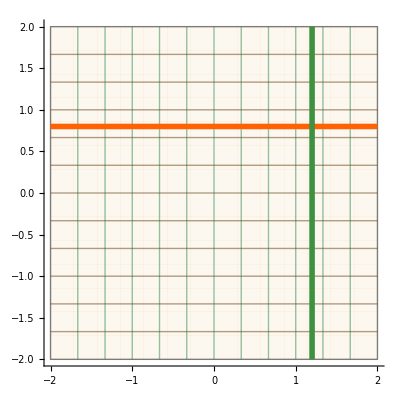
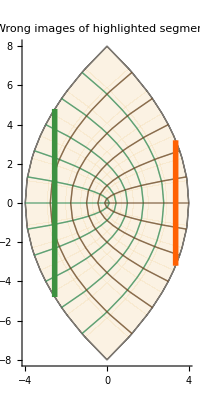

```mathematica
Row[
{Draw2D[{grid,horiz,vert},PlotRange->4,
Axes->True,ImageSize->Scaled[0.4]],
Draw2D[{{grid,horiz,vert}//ComplexMap[#^2&]},
PlotRange->8,Axes->True,
ImagePadding->{{0,0},{35,6}},
PlotLabel->"Wrong images\nof highlighted segments!",ImageSize->Scaled[0.4]]},Spacer[4]]
```

The parabolic arcs shown as the images of the horizontal and vertical segments of the grid are correct, but the images of the highlighted horizontal and vertical segments are wrong. The student, trying to generalize from the case of affine linear mappings, had unreasonable expectations as to what the application would do.

What went wrong is this. When using ComplexMap to form the image of the grid itself, Presentations applies the target function (here z↦z^2) to points along the lines of the grid and then connects the resulting image points in the codomain. For a primitive graphics object such as ComplexLine, however, it merely applies the function to distinguished points of the object—for ComplexLine, its vertices—and then forms the corresponding object in the codomain based upon the images of the distinguished points.

It was the encounter with this misunderstanding by students that led to the new Presentations primitive ComplexCurve to represent a curve in the complex plane parameterized by a real variable. The Presentations routines find the image of such a curve in the same way as for the lines in a grid—by sampling points along the curve, calculating their images, and then connecting the image points. The following modified curve, employing ComplexCurve objects, correctly represents the mapping.

```mathematica
grid={Opacity[0.5,HTML@Wheat],DrawCartesianMap[z, {z,-2(1+ⅈ),2(1+ⅈ)},
BoundaryStyle->Directive[Thick,Black],
Mesh->{11,11},MeshStyle->{HTML@SeaGreen,Darker@Brown}]};
horizontal={Legacy@CadmiumOrange, Thickness[0.015],ComplexCurve[(1-t)(-2+4ⅈ/5)+t( 2+4ⅈ/5),{t,0,1}]};
vertical={Legacy@CobaltGreen,Thickness[0.015],ComplexCurve[(1-s)(6/5-2ⅈ)+s(6/5+2ⅈ),{s,0,1}]};
```

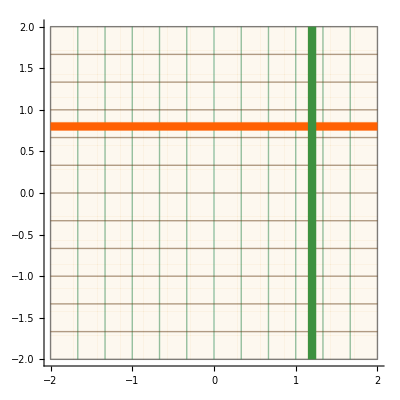
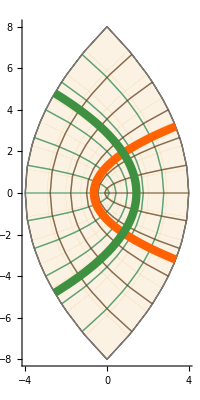

```mathematica
Row[
{Draw2D[{grid,horizontal,vertical},
PlotRange->4,Axes->True,ImageSize->Scaled[0.4]],Draw2D[{{grid,horizontal,vertical}//ComplexMap[#^2&]},PlotRange->8,Axes->True,ImageSize->Scaled[0.4]]},Spacer[4]]
```

Of course a rectangular grid is hardly the best way to understand how the squaring function maps. A polar grid, in this case covering a half-disk that we create first, is much better.

```mathematica
polargrid={Opacity[0.5,HTML@Wheat],
DrawPolarMap[z,{z,ComplexPolar[0,0],ComplexPolar[2,π]},
BoundaryStyle->Directive[Thick,Black],
Mesh->{5,9}, MeshStyle->{HTML@SeaGreen,Directive[Dashed,Darker@Brown]}]};
```

Then the plot produced by the following code would show that the squaring function doubles angles as it squares moduli. (The result has been suppressed.)

```mathematica
With[{arc={Legacy@CobaltGreen,Thickness[0.01],ComplexCurve[(5/3)Exp[ⅈ θ],{θ,0,π}]},
ray={Legacy@CadmiumOrange,Thickness[0.01],ComplexLine[{0,ComplexPolar[2,π/4]}]},
pts={ComplexCirclePoint[5/3,3,Black,Legacy@CadmiumOrange],ComplexCirclePoint[5ⅈ/3,3,Black,Legacy@LawnGreen]}},
Row[
{Draw2D[
{polargrid,ray,arc,pts},PlotRange->4.2,Axes->True,ImageSize->Scaled[0.4]],
Draw2D[{Arrowheads[0.25],NeedhamMappingSymbol[0,1],styleText[TraditionalForm[z^2],0.5+0.6ⅈ]},PlotRangeClipping->False,ImageSize->Scaled[0.06],ImagePadding->{{0,0},{25,10}}],
Draw2D[{
{polargrid,ray,arc,pts}//ComplexMap[#^2&]},PlotRange->4.2,Axes->True,ImageSize->Scaled[0.4]]},Spacer[5]];
]
```

With Mathematica, and its special dynamic features, it takes little extra work to convert such a static display into a dynamic presentation. We only have to keep in mind which parameters are going to be variable or dynamic, and so it is useful to develop the initial graphics within a Module or With expression that has the parameters as local variables.

```mathematica
Manipulate[
Module[{arc,ray,pts},
arc[r_]:={Legacy@CobaltGreen,Thickness[0.01],ComplexCurve[r Exp[ⅈ α],{α,0,π}]};
  ray[θ_]:={Legacy@CadmiumOrange,Thickness[0.01],ComplexLine[{0,ComplexPolar[2,θ]}]};
pts[r_,θ_]:={ComplexCirclePoint[r,4,Black,Legacy@CadmiumOrange],ComplexCirclePoint[ComplexPolar[r,θ],4,Black,Legacy@LawnGreen]};
Row[
{Draw2D[
{polargrid,ray[θ],arc[r],pts[r,θ]},PlotRange->4.2,Axes->True,ImageSize->Scaled[0.35]],
Draw2D[{Arrowheads[0.25],NeedhamMappingSymbol[0,1],styleText[TraditionalForm[z^2],0.5+0.6ⅈ]},PlotRangeClipping->False,ImageSize->Scaled[0.06],ImagePadding->{{0,0},{25,10}}],
Draw2D[{
{polargrid,ray[θ],arc[r],pts[r,θ]}//ComplexMap[#^2&]},PlotRange->4.2,Axes->True,ImageSize->Scaled[0.35]]},Spacer[5]]
],
{{r,5/3//N},0,2,Appearance->"Labeled"},{{θ,π/4//N},0,π,Appearance->"Labeled"}]
```

Similarly, the code could be modified to show dynamically what happens for varying powers z^n of z.

## Lifting Complex Mappings to the Riemann Sphere

Mapping properties of some complex functions may be nicely visualized by considering them as mappings of the Riemann sphere Ω. Let ℂ̂=ℂ∪{∞} be the extended complex plane, and let p:Ω→ℂ̂ be the stereographic projection onto the equatorial plane, with the north pole going to the point at infinity. To visualize the map p^-1:ℂ→Ω, consider the part A of the closed disk (D̄)_2(0) in the closed first quadrant.

First, we create a double polar grid on A to distinguish points inside the unit circle from points outside it and highlight parts of the boundary of A.

```mathematica
polargrids={Opacity[0.5,Legacy@Wheat],
DrawPolarMap[z,{z,ComplexPolar[0,0],ComplexPolar[1,π/2]},
BoundaryStyle->Directive[Thick,Legacy@DimGray],
Mesh->{5,8}, MeshStyle->{Legacy@RoyalBlue}],
DrawPolarMap[z,{z,ComplexPolar[1,0],ComplexPolar[2,π/2]},
BoundaryStyle->Directive[Thin,Legacy@DimGray],
Mesh->{5,8}, MeshStyle->{Legacy@IndianRed}]};
quarterCircle={Purple,Thickness[0.01],ComplexCurve[ⅇ^(ⅈ θ),{θ,0,π/2}]};
origin={Legacy@CadmiumOrange,PointSize[Large],ComplexPoint[0]};
xAxis={Legacy@CobaltGreen,Thickness[0.01],FineGrainLines[0.02,8][ComplexLine[{0,2}]]};
graphics2D={polargrids,quarterCircle,xAxis,origin};
```

The output from the following depicts both A and its image p^-1(A) on the Riemann sphere. Projection of the plane onto the sphere is handled by StereographicMap.

```mathematica
Manipulate[
Row[{Draw2D[{graphics2D},PlotRange->{{-1.15,2.15},{-0.15,2.15}},Axes->True,AxesStyle->Directive[Legacy@DimGray],Ticks->{Range[-1,2],Range[0,2]},ImageSize->Scaled[0.35]],
Draw3DItems[
{ColoredRiemannSphere[Opacity[0.15,Orange]],graphics2D//StereographicMap}//RotationTransformOp[θ,{0,0,1}],
ViewPoint->{1.27415,0.910696,0.695037},ViewRiemann,
ImageSize->Scaled[0.35]
]},Spacer[8]],
{{θ,0,"Rotation angle"},0,2π},FrameLabel->{None,None,Style["Mapping to the Riemann Sphere",FontWeight->Bold],None}]
```

In the first author’s course, stereographic projection had been described geometrically. When this graphic was demonstrated, students were curious to learn how the application implemented the projection. The explicit formula for StereographicMap appears in the ComplexGraphics package code, but students could not readily ferret that out. Using the application motivated the students to discover the formula and thereby presented an opportunity for them to exercise three-dimensional vector methods.

Our final example of visualizing complex functions as mappings is the complex sine. The following shows how sine maps a square grid in the z plane, with the image lifted to the Riemann sphere.

```mathematica
grid={Opacity[0.5,HTML@Linen],
DrawCartesianMap[z,{z,-π/2(1+ⅈ),π/2(1+ⅈ)},
BoundaryStyle->Directive[Thin,Black],
Mesh->{14,14},MeshStyle->{Legacy@DimGray,Legacy@DimGray}]};
points={PointSize[Large],Table[{Hue[0.1677j/20],ComplexPoint[-π+j π/10+0.95ⅈ]},{j,0,20}]};
positiveIAxis = {Legacy@MediumSeaGreen,Thick, ComplexCurve[ⅈ y, {y, 0, π}]};
primitives={grid,positiveIAxis,points};
```

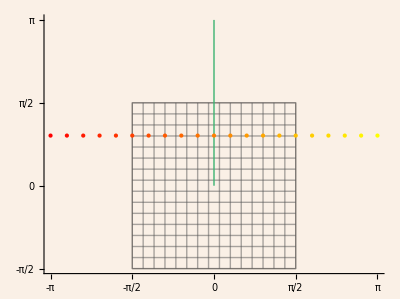
-Graphics--Graphics3D-

```mathematica
Row[{
Draw2D[{primitives},PlotRange->π,
Axes->True,AxesStyle->Legacy@DimGray,Ticks->{π/2 Range[-2,2],π/2 Range[-2,2]},
Background->Legacy@Linen,
ImageSize->Scaled[0.4]],
Draw3DItems[
{ColoredRiemannSphere[Opacity[0.2,Legacy@LightSkyBlue]],
{primitives}//ComplexMap[Sin]//StereographicMap},
ViewPoint->{0.991,-1.378,0.2579},ViewRiemann,Background->Opacity[0.25,Legacy@LightSkyBlue],
ImageSize->Scaled[0.4]]},Spacer[3]]
```

The grid is embellished with colored points. Sine is periodic of real period 2π, and nothing better illustrates this than the way the image wraps around the Riemann sphere, bringing the ends of the string of colored points together.

## Singularities

One way to visualize the behavior of a function f:ℂ→ℂ at singularities is to plot in 3-space the modulus|f|:ℂ→ℝ. This can be realized in a ComplexPolarSurface with second argument Abs. (More generally, a second argument σ for a function σ:ℂ→ℝ will provide a plot of the composite σ∘f:ℂ→ℝ. Other instructive cases are σ=Re and σ=Im.)

The following function has poles at z=-2, z=-1, z=1, z=ⅈ, and z=-ⅈ.

```mathematica
f[z_] := z Cos[z]/((z - 1)^2 (z^2 + 1)^2 (z^2 + 3z + 2) )
```

Due to the symmetry about the origin of two pairs of the poles of f, it is appropriate to plot over a polar region. The following plot depicts that lim_(z → z_0) |f(z)|=∞ at each pole z_0. (We could have used dynamic interactivity to zoom in on each pole.)

```mathematica
Draw3DItems[
{ColorMix[Legacy@MediumSeaGreen,White][0.2],
(* Draw the entire surface *)
ComplexPolarSurface[f[z],Abs,{z,ComplexPolar[0,0],ComplexPolar[3,2π],0},
Mesh->None],
(* Draw a fine-grained image in the region of the weak pole at -2 *)
ComplexPolarSurface[f[z],Abs,{z,ComplexPolar[1.75,170°],ComplexPolar[2.25,190°],0},
Mesh->None]},
PlotRange->{0,0.5},BoxRatios->{1,1,0.5},Axes->True,Background->Legacy@AliceBlue,
PlotLabel->Row[{"Surface plot of ",HoldForm[Abs[f[z]]]}],
ViewPoint->{0.3,-2.7,2.1}]
```

-Graphics3D-

The funnels at the poles appear to have different girths. The following calculation confirms that observation quantitatively.

```mathematica
poles=z/.Union[Solve[Denominator[f[z]]==0,z]];
Table[{Subscript[z, 0],
With[{Δ=0.05},
NIntegrate[f[z],{z,Subscript[z, 0]-Δ-ⅈ Δ,Subscript[z, 0]+Δ-ⅈ Δ,Subscript[z, 0]+Δ+ⅈ Δ,Subscript[z, 0]-Δ+ⅈ Δ,Subscript[z, 0]-Δ-ⅈ Δ}]//Abs]},{Subscript[z, 0],poles}]//TableForm
```

-2 | 0.023242
-1 | 0.212176
-ⅈ | 0.361677
ⅈ | 0.361677
1 | 0.479623

## Multifunctions

The next example, suggested by a problem in Needham [5, p. 117] uses functionality of Presentations that is more advanced than what might be introduced in a first course in complex analysis. It concerns the following complex function.

```mathematica
f[z_]:=√(z-1) (z-ⅈ)^(1/3)
```

The objective is to determine the nature of the branch points z=1 and z=ⅈ and how the function varies as we follow various paths in the complex plane. To do so we shall employ a different representation of a complex function that uses a single movable point z in the complex domain with an attached vector pointing from z to z+f(z).

First, we make a background plot on which to superimpose the moving complex vector.

```mathematica
backplot=ComplexPolarContour[f[z],{z,ComplexPolar[0,-π],ComplexPolar[3,π]},Abs,
PlotRange->3,
PlotPoints->{15,24},MaxRecursion->2,
ColorFunctionScaling->False,
Contours->Range[0,3,0.25],
ColorFunction->(ColorData["ThermometerColors"][Rescale[#,{0,3}]]&)];
```

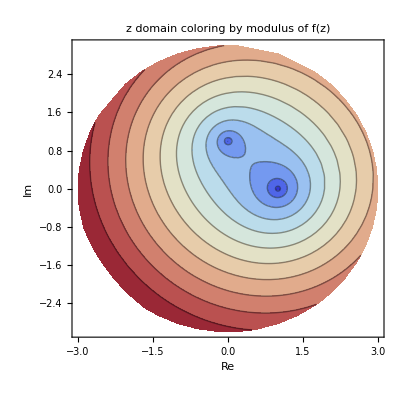

```mathematica
Draw2D[{backplot},
Frame->True,FrameLabel->{Re,Im},RotateLabel->False,
PlotLabel->Row[{TraditionalForm[z]," domain coloring by modulus of ",TraditionalForm[HoldForm[f[z]]]}]]
```

Strictly speaking, we do not need a background plot, but could just move a Locator around in the plane with perhaps a domain mesh. We could also choose between many different types of background plots. Although the information in the background plot is redundant, it does help orient the viewer, and modulus information is one of the best “orienters”.

In order to find all branches of the multifunction, we solve f(z)=w for w by taking sixth powers to clear the radical, so that the equation to be solved becomes w^6=(-1+z)^3(-ⅈ+z)^2.

```mathematica
wvalues=w/.Solve[f[z]^6==w^6,w]
```

{-√(-1+z) (-ⅈ+z)^(1/3),√(-1+z) (-ⅈ+z)^(1/3),-(-1)^(1/3) √(-1+z) (-ⅈ+z)^(1/3),(-1)^(1/3) √(-1+z) (-ⅈ+z)^(1/3),-(-1)^(2/3) √(-1+z) (-ⅈ+z)^(1/3),(-1)^(2/3) √(-1+z) (-ⅈ+z)^(1/3)}

The Presentations multifunction capability allows the generation of continuous sets of solutions along a path, even if a branch line is crossed. A path in the complex plane is first initialized using the Multivalues function. Multivalues has memory, and its first argument will routinely contain the values from the most recent evaluation. On initialization there are no previous values, so Null is supplied. The second argument is the list of expressions for the solutions and the third is the variable.

```mathematica
testpath=Multivalues[Null,wvalues,z];
```

We then calculate two successive values, which were conveniently picked to cross the branch line going from +1 to -∞. Successive sets of multivalues are calculated using the companion function CalculateMultivalues, which carries the particular pathname as a subvalue. The routine returns the list of values and the permutation of the solutions used for those values.

```mathematica
CalculateMultivalues[testpath][0.]
CalculateMultivalues[testpath][-.01ⅈ]
```

{{-0.5-0.866025 ⅈ,0.5+0.866025 ⅈ,0.5-0.866025 ⅈ,-0.5+0.866025 ⅈ,1.-1.66533×10^-16 ⅈ,-1.+1.66533×10^-16 ⅈ},{1,2,3,4,5,6}}

{{-0.497323-0.871422 ⅈ,0.497323+0.871422 ⅈ,0.506012-0.866405 ⅈ,-0.506012+0.866405 ⅈ,1.00333+0.00501655 ⅈ,-1.00333-0.00501655 ⅈ},{2,1,4,3,6,5}}

Note that the values have been permuted between the two solutions and that all the solutions from the second evaluation are close to the solutions from the first evaluation. Often we will only be interested in the first solution that is generated. The following generates a table of values of the first solution as testpath circles the branch point at z=1. For multivalues with memory to work properly, the steps on the path should be reasonably close. Here they are just close enough to work and yet give a short output list of angle, first function value, and permutation used.

```mathematica
testpath=Multivalues[Null,wvalues,z];
Column@(Table[{θ,First@First[#],Last[#]}&@CalculateMultivalues[testpath][1+0.2 ⅇ^(ⅈ θ)],{θ,0,2π,2π/12}]
⟦{1,7,8,9,13}⟧)  (* sample path to indicate change *)
```

{0,-0.505044+0.119094 ⅈ,{1,2,3,4,5,6}}
{π,-0.142909-0.464146 ⅈ,{1,2,3,4,5,6}}
{(7 π)/6,-0.0233462-0.496879 ⅈ,{2,1,4,3,6,5}}
{(4 π)/3,0.110254-0.497419 ⅈ,{2,1,4,3,6,5}}
{2 π,0.505044-0.119094 ⅈ,{2,1,4,3,6,5}}

Note that a complete circuit has reversed the function value. As we will show, it takes two complete circuits to return to the original function value.

In the following presentation a background graphic consisting of a contour plot of the modulus |f(z)| is given to provide some overall orientation for the viewer. A locator is provided as a red CirclePoint. This can be used to sample f at any point included in the domain of the graphic. Attached to the locator is a vector that gives the value of the first solution (at half scale) of w=f(z) at that point. On the right of the graphic, the numerical values of z and f(z) are given, in Cartesian and polar form. The notation r ∠θ is the form returned by the Presentations function ComplexPolar[r,θ] to represent the polar form r ⅇ^(ⅈ θ), in other words, the value of PolarToComplex[ComplexPolar[r,θ]].

```mathematica
DynamicModule[{zpt={1.,1.65},w,root},
Module[
{f=Function[z,√(z-1) (z-ⅈ)^(1/3)],wvalues,z},
wvalues=Multivalues[Null,w/.Solve[w^6==f[z]^6,w],z];
Row[
{Draw2D[
{backplot,
Dynamic@Arrow[{zpt,zpt+1/2ToCoordinates[root=Extract[CalculateMultivalues[wvalues][ToComplex[zpt]],{1,1}]]}],
Locator[Dynamic[zpt],Graphics[{CirclePoint[{0,0},3,Black,Red]}]]},
Frame->True,FrameLabel->{Re,Im},RotateLabel->False,
PlotRange->3,
PlotLabel->Row[{f["z"],"\n as a Riemann Surface"}],
Background->None,ImageSize->Scaled[0.5]],
Dynamic@Column[
{ComplexArgumentPanel[ToComplex[zpt],{True,True,False},"z",{Top,Left},ImageSize->Scaled[0.45]],Spacer[10],
ComplexArgumentPanel[root,{True,True,False},Row[{f["z"]}],{Top,Left},ImageSize->Scaled[0.45]]}] (* Column *)},
Spacer[10]] (* Row *)]
]
```

-Graphics-1.+1.65 ⅈ
1.92938∠1.02593 (58.7816°)z

-0.761593-1.12945 ⅈ
1.36223∠-2.16407 (-123.992°)√(-1+z) (-ⅈ+z)^(1/3)

Dragging the locator around the branch points demonstrates the multivalued nature of f. The locator must be dragged twice around the point z=1, or three times around the point z=ⅈ, in order to return to its original value. It must be dragged six times around the complex of both branch points in order to return to its original value. This illustrates that it is not possible to have only a single branch line that joins the two branch points. There must be at least one branch line that goes to infinity.

Another way to present the same situation, carried out in [Reference], would be to attach all six solution vectors to each point in an array. But it is amazing how much information can be obtained with a single movable point and a single continuous solution. This is a true four-dimensional representation, although a local one: the domain of the function provides two dimensions, and the vector provides two more dimensions. By moving the locator, the complete four dimensions are revealed. Lastly, by showing only a single solution, we are in effect moving on the function’s Riemann surface, where the function is single-valued. By moving to various points on the surface we can recover all of the values. Thus we can explore the entire surface and return to a starting point with no discontinuities and no artifacts of intersecting surfaces. Of course we do not see the surface as an object in four-dimensional space; it just smiles at us like the Cheshire cat.

The Riemann surface is a complex surface. One way to visualize it as surface-like in real three-dimensional space is to represent it as a ComplexPolar object but, instead of r and θ as arguments, use graphical objects that give the modulus and argument of the surface.

```mathematica
Column[{Style["Riemann surface =",FontFamily->"Helvetica"],
Row[{
Draw3DItems[
{Opacity[0.8,HTML@SteelBlue],
Table[ComplexPolarSurface[w,Abs,{z,ComplexPolar[0,-π],ComplexPolar[3,π]},
Mesh->{3,24}],{w,wvalues}]},
NeutralLighting[0,0.6,0.2],NiceRotation,
PlotLabel->Row[{"Modulus of ",f[z]}],
ViewPoint->{2.1421,0.695506,0.133009},Boxed->False,
ImageSize->Scaled[0.4]
],
Style[Row[{"∠"}],24],
Draw3DItems[
{Opacity[0.8,Orange],
Table[ComplexPolarSurface[w,Arg,{z,ComplexPolar[0,-π],ComplexPolar[3,π]},
Mesh->{3,24}],{w,wvalues}]},
NeutralLighting[0,0.6,0.2],NiceRotation,
PlotLabel->Row[{"Argument of ",f[z]}],
ViewPoint->{2.1421,0.695506,0.133009},Boxed->False,
ImageSize->Scaled[0.4]
]}]
},Alignment->Center,Spacings->1]
```

Riemann surface =
-Graphics3D-∠-Graphics3D-

For aesthetic reasons the Box and Axes for the images were suppressed. There is one artifact in this presentation: in the argument graphic we must identify the upper edges (which occur at π) with the corresponding lower edges (which occur at -π). Moreover, it is quite difficult to trace the paths that were used around the branch points in the previous, vector-locator, presentation. Perhaps a better presentation is obtained by a picture that looks more closely about one of the branch points, for example, z=1.

```mathematica
Column[{Style["Riemann surface =",FontFamily->"Helvetica"],
Row[{
Draw3DItems[
{Opacity[0.8,HTML@SteelBlue],
Table[ComplexPolarSurface[w,Abs,{z,ComplexPolar[0,-π],ComplexPolar[0.2,π],1},
Mesh->{3,24}],{w,wvalues}]},
NeutralLighting[0,0.6,0.2],
NiceRotation,
PlotLabel->Row[{"Modulus of ",f[z]}],Boxed->False,
ViewPoint->{2.1421,0.695506,0.133009},
ImageSize->Scaled[0.4]
],
Style[Row[{"∠"}],24],
Draw3DItems[
{{Opacity[0.6,Orange],
Table[ComplexPolarSurface[w,Arg,{z,ComplexPolar[0,-π],ComplexPolar[0.2,π],1},
Mesh->{3,24}],{w,Part[wvalues,{1,2}]}]},
{Opacity[0.6,Blue],
Table[ComplexPolarSurface[w,Arg,{z,ComplexPolar[0,-π],ComplexPolar[0.2,π],1},
Mesh->{3,24}],{w,Part[wvalues,{3,4}]}]},
{Opacity[0.6,Green],
Table[ComplexPolarSurface[w,Arg,{z,ComplexPolar[0,-π],ComplexPolar[0.2,π],1},
Mesh->{3,24}],{w,Part[wvalues,{5,6}]}]}},
NeutralLighting[0,0.6,0.2],
NiceRotation,
PlotLabel->Row[{"Argument of ",f[z]}],
ViewPoint->{2.1421,0.695506,0.133009},Boxed->False,BoxRatios->{1,1,1},
ImageSize->Scaled[0.4]
]}]
},Alignment->Center,Spacings->1]
```

Riemann surface =
-Graphics3D-∠-Graphics3D-

Viewed closely about the point z=1, the Riemann argument surface appears as three separate surfaces, each of which requires two revolutions to return to the original value. Go back to the dynamic vector-locator presentation. Circle closely around the zero at 1 and you will see one of the surfaces. Now take a detour around the other zero at ⅈ and return to circling the zero at 1. You will be on a different surface. Take one more detour and you will be on the third surface. This behavior might not have been discovered from the vector-locator presentation alone. Multiple presentations that complement each other are often the route to a fuller understanding of the beauty of complex functions.

Visualizing Riemann surfaces of multifunctions by means of surfaces in three-dimensional space also appears in [Reference].

## The Argument Principle

Domain coloring may also be used to visualize general principles about complex functions. We illustrate this with an adaptation of an example by Lundmark [Reference] concerning the Argument Principle. (Lundmark also provides online examples of similar types of domain-coloring plots created using tools other than Mathematica.)

The following function has a pole of order 3 at z=0, a zero of order 2 at z=2, and zeros of order 1 at z=-2-2ⅈ and -1+2ⅈ.

```mathematica
f[z_]:=(z-2)^2(z+1-2ⅈ)(z+2+2ⅈ)/z^3
```

To illustrate the Argument Principle, we shall construct a graphic in two stages. In the first stage we construct a background graphic that is colored according to the argument of the function and then superimpose modulus contours on top of that. The function DomainColoring can generally be used for three-color coloring to indicate argument and modulus simultaneously. But here we use it with an ArgColor routine that colors from IndianRed to Yellow as the argument varies from 0 to 2π. (This results from the “0” argument in ArgColor that specifies the branch point in the z domain to be at 0 radians. Normally it is at -π.) Finally, ComplexCartesianContour is used to plot a selected set of modulus contours without any contour shading so that they overlay the argument coloring.

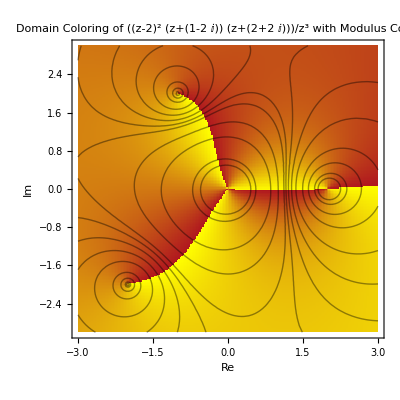

```mathematica
With[
{zmin=-3(1+ⅈ),zmax=3(1+ⅈ),
colorfunction=ArgColor[Legacy@IndianRed,Yellow,Black,Legacy@Smoke][0]},
Draw2D[
{background=
{DomainColoring[f[z],{z,zmin,zmax},colorfunction,PlotPoints->200],
ComplexCartesianContour[f[z],{z,zmin,zmax},Abs,
Contours->{0.1,0.2,0.5,1,2,3,4,5,6,10,20,100,200},
ContourShading->None,
PlotRange->{0,250}]}},
PlotRange->3,
Frame->True,FrameLabel->{Re, Im},RotateLabel->False,
PlotLabel->Row[{"Domain Coloring of ",f[z],"\n with Modulus Contours"}]]
]
```

In the second stage of constructing the graphic, upon that background we plot two simple closed curves, the first around the points z=2 and z=-1+2ⅈ, and the second around z=0 and z=-2-2ⅈ. (In Mathematica 5 these points were obtained by clicking and copying points. In Mathematica 6 they could be obtained by using the LocatorLine routine in Presentations that allows any number of locators to be positioned on the graphic and used to copy their coordinates.) Each of the branch points is labeled with its signed multiplicity, a positive sign denoting a zero and a negative sign denoting a pole.

```mathematica
poleszeros={2,-1+2ⅈ,-2-2ⅈ,0};offset=-0.1+0.2ⅈ;
```

```mathematica
circuit1=SplineToLine[{{0.342528,-0.32536},{0.369328,0.492018},{0.020937,1.3094},{-0.809841,1.2826},{-1.60042,0.43842},{-2.2436,-0.633552},{-2.4044,-1.47773},{-2.458,-2.20131},{-1.52002,-2.5497},{-0.421251,-2.05391},{0.181733,-1.08914},{0.342528,-0.32536}},Cubic,40];
circuit2=SplineToLine[{{2.51327,0.0632296},{2.27208,0.626015},{1.92369,1.229},{1.5351,1.63099},{1.06611,2.01958},{0.302329,2.38137},{-0.582047,2.54216},{-1.41282,2.48856},{-1.62722,2.05978},{-1.58702,1.64439},{-1.30563,1.44339},{-0.943837,1.53719},{-0.488249,1.69799},{-0.113059,1.72479},{0.168333,1.56399},{0.530123,1.2692},{0.771317,0.894007},{0.918713,0.398221},{1.15991,-0.124365},{1.5351,-0.512955},{2.07108,-0.620152},{2.48647,-0.298561},{2.51327,0.0632296}},Cubic,50];
```

```mathematica
With[
{zmin=-3(1+ⅈ),zmax=3(1+ⅈ),
colorfunction=ArgColor[Legacy@IndianRed,Yellow,Black,Legacy@Smoke][]},
Draw2D[
{background,
ComplexCirclePoint[#1,4,Black,Legacy@SkyBlue]&/@{2,-(1-2 ⅈ),-(2+2 ⅈ)},ComplexCirclePoint[0,5,Black,Blue],
AbsoluteThickness[2],Arrowheads[{{0.06,0.8}}],Legacy@DodgerBlue,Arrow[circuit1],
Legacy@SeaGreen,Arrowheads[{{0.06,0.2}}],Arrow[circuit2],
Black,
MapThread[ComplexText[Style[#2,FontSize->14,FontWeight->"Bold"],#1]&,{offset+poleszeros,{2,1,1,-3}}]},
PlotRange->3,
Frame->True,FrameLabel->{Re, Im},
PlotLabel->Row[{"Domain Coloring of ",f[z],"\n with Modulus Contours"}]]
]
```

-Graphics-

As the argument coloring indicates, as z makes a circuit of each simple closed curve, the number of times the argument of f(z) increments by 2π equals the sum of the orders of the zeros and poles inside that curve. And that is precisely what, according to the Argument Principle, happens in general for a meromorphic function f: Let γ be a positively oriented, simple closed curve that does not pass through any zeros or poles of f. As z winds around γ, the image curve f∘γ winds N-P times around w=0, where N is the number of zeros of f inside γ and P is the number of poles inside γ, where each zero and pole is counted as many times as its multiplicity.

## Conclusion

Ideally, students coming to a complex analysis course where Presentations is used would already be experienced with Mathematica. In reality, unfortunately, this is seldom the case: students must learn Mathematica fundamentals with specifics about Presentations as they are learning about complex numbers and complex functions. In the first-named author’s course, two days’ class time was spent in a laboratory setting with a hands-on, rapid introduction to Mathematica, including a first glimpse of some functionality of Cardano3 that is now in Presentations. Although that arrangement was hardly optimal, it sufficed to get them started.

To a Mathematica novice, the syntax of graphics routines in Cardano3, with their multiple, deeply-nested list arguments, was daunting. In the first author’s course, few students succeeded in constructing a syntactically correct domain-codomain mapping graphic without direct access to the documentation; they therefore relied upon instructor-provided templates for their own work.

As a result of that teaching experience of the first author and the entirely new features introduced with Mathematica 6, the Cardano3 routines were completely redesigned and rewritten and then incorporated in the Presentations application, the successor to DrawGraphics. One major flaw in the Cardano3 design was an attempt to create a container and user interface that would handle all complex-function graphics. It is now recognized that packages should not create new interfaces, which are just additional specialized things that students have to learn, but should instead simply extend Mathematica and mesh with its standard usage.

Until such a time as technical students can begin learning Mathematica in secondary school, it will remain a challenge to bring them up to speed for Mathematica use in college courses. A temporary and imperfect, but still useful, alternative could be to provide the kinds of examples shown here as webMathematica applications or Demonstrations (demonstrations.wolfram.com). For now the best solution may be specially designed Mathematica tutorials that present the common constructions used in the course and introductory labs. But there is a wonderful payoff when students can obtain hands-on visual experience of the mathematical objects to complement their analytical work.

## References

D. J. M. Park, Jr. “Presentations Package for Mathematica: Custom Graphics and Presentations with Mathematica.” (Dec 12, 2007) home.comcast.net/~djmpark/DrawGraphicsPage.html.

D. J. M. Park, Jr. “Cardano3 Package.” (Jun 19, 2006) home.comcast.net/~djmpark/Cardano3Page.html.

M. Eisenberg. “Math 421—Fall 2006: Complex Variables.” (Jan 7, 2007).

J. H. Mathews and R. W. Howell, Complex Analysis for Mathematics and Engineering, 5th ed., Sudbury, MA: Jones and Bartlett Publishers, 2006.

T. Needham, Visual Complex Analysis, New York: Oxford University Press, 1997.

D. J. M. Park, Jr., “DrawGraphics,” Mathematica in Education and Research, 10(1), 2005 pp. 41–66.

T. Ersek. “RootSearch Looks for All Roots of an Equation between xmin and xmax.” (May 2, 2006) library.wolfram.com/infocenter/MathSource/4482.

S. Kivelä, “On the Visualization of Riemann Surfaces,” in Applied Mathematica, Electronic Proceedings of the Eighth International Mathematica Symposium (IMS’06), Avignon, France (Y. Papegay, ed.), Sophia Antipolis, France: INRIA, 2006 ISBN 2-7261-1289-7. internationalmathematicasymposium.org/IMS2006/IMS2006_CD/html/articles.html.

H. Lundmark. “Hans Lundmark’s Complex Analysis Pages.” (Jan 28, 2008) 
www.mai.liu.se/~halun/complex.

M. Eisenberg and D. J. M. Park, Jr., “Visualizing Complex Functions with the Cardano3 Application,” in Applied Mathematica, Electronic Proceedings of the Eighth International Mathematica Symposium (IMS’06), Avignon, France (Y. Papegay, ed.), Sophia Antipolis, France: INRIA, 2006 ISBN 2-7261-1289-7 
internationalmathematicasymposium.org/IMS2006/IMS2006_CD/html/articles.html.

Anonymous. “MathGroup Archive 2006.” (Feb 2006) 
forums.wolfram.com/mathgroup/archive/2006/Feb/msg00336.html.

M. Eisenberg and D. J. M. Park, Jr., “Visualizing Complex Functions with the Presentations Application,” The Mathematica Journal, 2011. doi:10.3888/tmj.11.2–6.

About the Authors

Murray Eisenberg is a professor of mathematics and statistics at the University of Massachusetts Amherst and received his A.B. and A.M. from the University of Pennsylvania and his Ph.D. from Wesleyan University. Eisenberg’s principal mathematical interest is the topology of dynamical systems. He has published articles on topological dynamics, the APL and J programming languages, and the use of computers in teaching undergraduate mathematics, and is the author of three undergraduate textbooks.

David J. M. Park, Jr. received a B.S. and M.S. in electrical engineering from M.I.T. Park worked on microwave and beam design elements of early cesium beam tubes for atomic clocks and on masers. While working as a computer consultant he became involved in biochemistry and developmental biology, published a number of articles in the field, and worked for a period of time at the Laboratory for Theoretical Biology at N.I.H. In his retirement he has used Mathematica to renew an interest in mathematical physics and in the process has developed packages used by many Mathematica users. Most recently he has been collaborating with Renan Cabrera and Jean-François Gouyet to design Tensorial, a Mathematica package for tensor calculus.

Murray Eisenberg
Department of Mathematics and Statistics
University of Massachusetts
Lederle Graduate Research Tower
710 North Pleasant Street
Amherst, MA 01003-9305 USA
murray@math.umass.edu
www.math.umass.edu/~murray

David J. M. Park, Jr.
1429 Searchlight Way
Mount Airy, MD 21771 USA
djmpark@comcast.net
home.comcast.net/~djmpark